# Omicron analysis: Plotting partitioned case counts and Rt

## Splitting out lineage BA.1 / clade 21K from lineage BA.2 / clade 21L

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/omicron-countries-split

```mathematica
dataset="omicron-countries-split";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=250;
```

```mathematica
gridCount=4;
```

## Setup

### Variants

```mathematica
variants={"other","Delta","Omicron 21K","Omicron 21L"};
```

```mathematica
n=Length[variants]
```

4

### Colors

```mathematica
colors=Prepend[Table[ColorData["Rainbow"][i],{i,{0.3,0.7,0.95}}],Gray]
```

{GrayLevel[0.5],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.8083415999999999, 0.7110806000000001, 0.255976],RGBColor[0.8739574, 0.2607876000000001, 0.15481040000000004]}

```mathematica
legendPanel=PointLegend[colors,variants,LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}]
```

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-11-01","2021-12-01","2022-01-01","2022-02-01"};
```

### Smoothing functions

```mathematica
smoothed[dateSeries_]:=Map[{#[[4,1]],N[Mean[#[[All,2]]]]}&,Partition[dateSeries,7,1]]
```

```mathematica
simplePrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[1]],N[(#1[[2]])/(0.0001+#2[[2]])]}&,{dateSeriesPositives,dateSeriesTotals}]
```

```mathematica
smoothedPrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[4,1]],N[Total[#1[[All,2]]]/(0.0001+Total[#2[[All,2]]])]}&,{Partition[dateSeriesPositives,7,1],Partition[dateSeriesTotals,7,1]}]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

### Countries

```mathematica
countriesToDrop={"Czech Republic"};
```

## Rt estimates

Using GARW (growth autoregressive random walk) model

```mathematica
rtData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_Rt-combined-"<>model<>".tsv"];
```

```mathematica
header=rtData[[1]]
```

{date,location,variant,median_R,median_freq,R_upper_95,R_lower_95,R_upper_80,R_lower_80,R_upper_50,R_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_R→4,median_freq→5,R_upper_95→6,R_lower_95→7,R_upper_80→8,R_lower_80→9,R_upper_50→10,R_lower_50→11}

```mathematica
rtData=Drop[rtData,1];
```

```mathematica
startDate=First[Sort[rtData[[All,1]]]]
```

2021-10-15

```mathematica
modelEndDate=Last[Sort[rtData[[All,1]]]]
```

2022-02-22

```mathematica
endDate=Last[Sort[rtData[[All,1]]]]
```

2022-02-22

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
countries=Union[rtData[[All,2]]]
```

{Australia,Austria,Belgium,Canada,Czech Republic,Denmark,France,Germany,India,Indonesia,Ireland,Israel,Italy,Japan,Netherlands,New Zealand,Norway,Poland,Portugal,Romania,Singapore,South Africa,Spain,Sweden,Switzerland,Thailand,United Kingdom,USA}

```mathematica
countries=DeleteCases[countries,x_/;MemberQ[countriesToDrop,x]]
```

{Australia,Austria,Belgium,Canada,Denmark,France,Germany,India,Indonesia,Ireland,Israel,Italy,Japan,Netherlands,New Zealand,Norway,Poland,Portugal,Romania,Singapore,South Africa,Spain,Sweden,Switzerland,Thailand,United Kingdom,USA}

Only keep Rt data points when the variant is frequent enough to have a good estimate

```mathematica
rtData=Cases[rtData,x_/;x[[5]]>0.005];
```

```mathematica
rtData=DeleteCases[rtData,x_/;x[[2]]=="South Africa"&&x[[5]]<0.01];
```

```mathematica
rtGather[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
rtGatherLower[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,9}]]
```

```mathematica
rtGatherUpper[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
variantCountryRtPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=rtGather[country,variant];
lowerSeries=rtGatherLower[country,variant];
upperSeries=rtGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{35,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,4.5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,0}],Dashed,Black,Line[{{startDate,1},{modelEndDate,1}}]}]
]
```

```mathematica
variantsCountryRtLabelPlot[country_,variants_]:=Module[{medians,finalDates,finalValues},
medians=Map[Last[rtGather[country,#]]&,variants];
finalDates=medians[[All,1]];
finalValues=medians[[All,2]];
DateListPlot[{},Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{30,5},{15,10}},PlotRange->{{startDate,DatePlus[modelEndDate,10]},
{0,4.5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Prolog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],MapThread[Text[Style[NumberForm[Round[#2,0.1],{2,1}],Black,FontSize->10,FontFamily->"Helvetica"],{DatePlus[#1,1],#2},{-1,0}]&,{finalDates,finalValues}],Dashed,Black,Line[{{startDate,1},{modelEndDate,1}}]}]
]
```

```mathematica
countryRtPlot[country_]:=Show[variantsCountryRtLabelPlot[country,variants[[2;;4]]],Table[variantCountryRtPlot[country,variants[[i]],colors[[i]]],{i,2,4}]]
```

```mathematica
panels=Map[countryRtPlot,countries];
```

```mathematica
legendPanel=PointLegend[colors[[2;;4]],variants[[2;;4]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

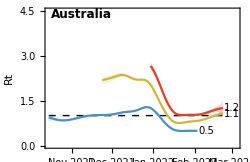
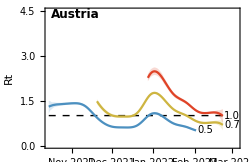
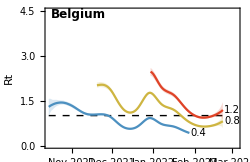
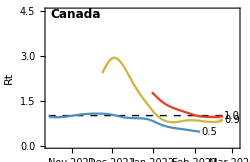
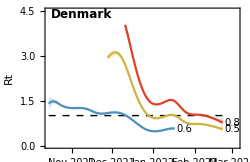
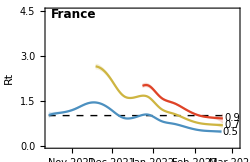
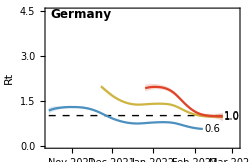
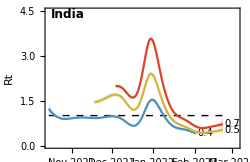
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries-split_variant-rt.png

Rt

```mathematica
Map[#->{rtGather[#,"Omicron 21L"][[-1,1]],Round[rtGather[#,"Omicron 21L"][[-1,2]],0.1],Round[rtGatherLower[#,"Omicron 21L"][[-1,2]],0.1],Round[rtGatherUpper[#,"Omicron 21L"][[-1,2]],0.1]}&,countries]
```

{Australia→{2022-02-22,1.2,1.,1.5},Austria→{2022-02-22,1.,0.7,1.2},Belgium→{2022-02-22,1.2,0.9,1.5},Canada→{2022-02-22,1.,0.8,1.1},Denmark→{2022-02-22,0.8,0.6,0.9},France→{2022-02-22,0.9,0.8,1.1},Germany→{2022-02-22,1.,0.8,1.1},India→{2022-02-22,0.7,0.5,0.9},Indonesia→{2022-02-22,1.1,0.9,1.3},Ireland→{2022-02-22,1.,0.6,1.3},Israel→{2022-02-22,0.8,0.6,0.9},Italy→{2022-02-22,1.2,1.,1.4},Japan→{2022-02-22,1.,0.7,1.2},Netherlands→{2022-02-22,0.8,0.6,0.9},New Zealand→{2022-02-22,2.,1.6,2.3},Norway→{2022-02-22,1.,0.8,1.2},Poland→{2022-02-22,1.,0.9,1.2},Portugal→{2022-02-22,1.1,0.9,1.4},Romania→{2022-02-22,1.,0.8,1.3},Singapore→{2022-02-22,1.2,0.9,1.5},South Africa→{2022-02-22,1.1,0.8,1.3},Spain→{2022-02-22,1.,0.8,1.1},Sweden→{2022-02-22,1.,0.8,1.3},Switzerland→{2022-02-22,1.1,0.9,1.2},Thailand→{2022-02-22,1.4,1.1,1.6},United Kingdom→{2022-02-22,1.1,0.9,1.2},USA→{2022-02-22,1.3,1.1,1.4}}

## Little r estimates

Using fixed growth model

```mathematica
rData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_little-r-combined-"<>model<>".tsv"];
```

```mathematica
header=rData[[1]]
```

{date,location,variant,median_r,median_freq,r_upper_95,r_lower_95,r_upper_80,r_lower_80,r_upper_50,r_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_r→4,median_freq→5,r_upper_95→6,r_lower_95→7,r_upper_80→8,r_lower_80→9,r_upper_50→10,r_lower_50→11}

```mathematica
rData=Drop[rData,1];
```

Only keep Rt data points when the variant is frequent enough to have a good estimate

```mathematica
rData=Cases[rData,x_/;x[[5]]>0.005];
```

```mathematica
rData=DeleteCases[rData,x_/;x[[2]]=="South Africa"&&x[[5]]<0.01];
```

```mathematica
rGather[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
rGatherLower[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,9}]]
```

```mathematica
rGatherUpper[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
variantCountryLittleRPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=rGather[country,variant];
lowerSeries=rGatherLower[country,variant];
upperSeries=rGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{45,5},{15,10}},Joined->True,PlotRange->{{startDate,DatePlus[modelEndDate,7]},
{-0.35,0.4}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,0}],Dashed,Black,Line[{{startDate,0},{modelEndDate,0}}]}]
]
```

```mathematica
variantsCountryLittleRLabelPlot[country_,variants_]:=Module[{medians,finalDates,finalValues},
medians=Map[Last[rGather[country,#]]&,variants];
finalDates=medians[[All,1]];
finalValues=medians[[All,2]];
DateListPlot[{},Frame->{True,True,False,False},FrameLabel->{"","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{42,5},{15,10}},PlotRange->{{startDate,DatePlus[modelEndDate,16]},
{-0.35,0.4}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Prolog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],MapThread[Text[Style[NumberForm[Round[#2,0.01],{2,2}],Black,FontSize->10,FontFamily->"Helvetica"],{DatePlus[#1,1],#2},{-1,0}]&,{finalDates,finalValues}],Dashed,Black,Line[{{startDate,0},{modelEndDate,0}}]}]
]
```

```mathematica
countryLittleRPlot[country_]:=Show[variantsCountryLittleRLabelPlot[country,variants[[2;;4]]],Table[variantCountryLittleRPlot[country,variants[[i]],colors[[i]]],{i,2,4}]]
```

```mathematica
panels=Map[countryLittleRPlot,countries];
```

```mathematica
legendPanel=PointLegend[colors[[2;;4]],variants[[2;;4]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

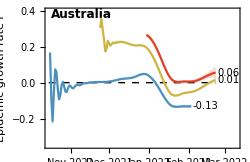
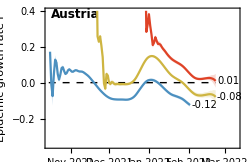
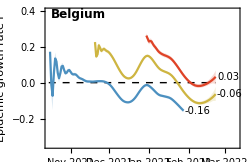
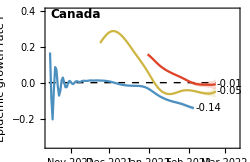
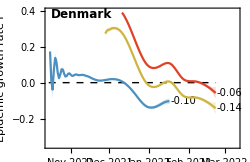
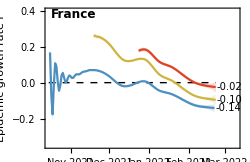
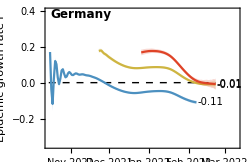
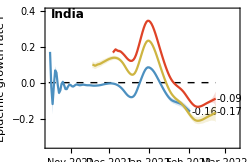
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-little-r.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries-split_variant-little-r.png

Little r

```mathematica
Map[#->{rGather[#,"Omicron 21L"][[-1,1]],Round[rGather[#,"Omicron 21L"][[-1,2]],0.01],Round[rGatherLower[#,"Omicron 21L"][[-1,2]],0.01],Round[rGatherUpper[#,"Omicron 21L"][[-1,2]],0.01]}&,countries]
```

{Australia→{2022-02-22,0.06,0.02,0.09},Austria→{2022-02-22,0.01,-0.03,0.05},Belgium→{2022-02-22,0.03,-0.01,0.07},Canada→{2022-02-22,-0.01,-0.04,0.02},Denmark→{2022-02-22,-0.06,-0.09,-0.02},France→{2022-02-22,-0.02,-0.05,0.01},Germany→{2022-02-22,-0.01,-0.04,0.02},India→{2022-02-22,-0.09,-0.13,-0.05},Indonesia→{2022-02-22,0.02,0.,0.05},Ireland→{2022-02-22,0.01,-0.05,0.06},Israel→{2022-02-22,-0.06,-0.1,-0.02},Italy→{2022-02-22,0.05,0.02,0.08},Japan→{2022-02-22,-0.01,-0.04,0.03},Netherlands→{2022-02-22,-0.07,-0.1,-0.03},New Zealand→{2022-02-22,0.18,0.15,0.21},Norway→{2022-02-22,-0.01,-0.05,0.02},Poland→{2022-02-22,0.01,-0.02,0.03},Portugal→{2022-02-22,0.03,-0.01,0.06},Romania→{2022-02-22,0.,-0.04,0.03},Singapore→{2022-02-22,0.05,0.01,0.1},South Africa→{2022-02-22,0.01,-0.02,0.05},Spain→{2022-02-22,0.,-0.03,0.03},Sweden→{2022-02-22,-0.01,-0.05,0.03},Switzerland→{2022-02-22,0.02,0.,0.04},Thailand→{2022-02-22,0.07,0.04,0.1},United Kingdom→{2022-02-22,0.02,-0.01,0.04},USA→{2022-02-22,0.06,0.03,0.09}}

Doubling time

```mathematica
Map[#->{rGather[#,"Omicron 21L"][[-1,1]],Round[Log[2]/rGather[#,"Omicron 21L"][[-1,2]],0.1],Round[Log[2]/rGatherUpper[#,"Omicron 21L"][[-1,2]],0.1],Round[Log[2]/rGatherLower[#,"Omicron 21L"][[-1,2]],0.1]}&,countries]
```

{Australia→{2022-02-22,12.4,7.9,34.4},Austria→{2022-02-22,71.4,14.,-25.1},Belgium→{2022-02-22,21.4,10.1,-68.2},Canada→{2022-02-22,-84.3,35.1,-19.5},Denmark→{2022-02-22,-12.,-32.6,-7.7},France→{2022-02-22,-28.4,76.,-12.8},Germany→{2022-02-22,-97.9,31.1,-17.9},India→{2022-02-22,-7.8,-14.,-5.4},Indonesia→{2022-02-22,28.1,12.9,-151.6},Ireland→{2022-02-22,101.6,11.7,-14.1},Israel→{2022-02-22,-12.1,-40.,-7.1},Italy→{2022-02-22,13.8,8.7,31.9},Japan→{2022-02-22,-66.5,27.2,-15.4},Netherlands→{2022-02-22,-10.5,-21.6,-6.7},New Zealand→{2022-02-22,3.9,3.3,4.7},Norway→{2022-02-22,-77.5,30.3,-15.3},Poland→{2022-02-22,136.6,27.3,-42.6},Portugal→{2022-02-22,27.3,11.5,-61.8},Romania→{2022-02-22,-155.7,21.3,-16.},Singapore→{2022-02-22,13.2,7.1,61.},South Africa→{2022-02-22,63.3,14.5,-28.4},Spain→{2022-02-22,-315.2,25.7,-20.9},Sweden→{2022-02-22,-60.1,22.1,-12.8},Switzerland→{2022-02-22,29.5,15.7,381.7},Thailand→{2022-02-22,9.8,6.7,16.1},United Kingdom→{2022-02-22,39.3,15.6,-68.5},USA→{2022-02-22,11.8,7.9,24.2}}

## Prevalence

Using fixed growth model

```mathematica
pData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_I-combined-"<>model<>".tsv"];
```

```mathematica
header=pData[[1]]
```

{date,location,variant,median_I,I_upper_95,I_lower_95,I_upper_80,I_lower_80,I_upper_50,I_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_I→4,I_upper_95→5,I_lower_95→6,I_upper_80→7,I_lower_80→8,I_upper_50→9,I_lower_50→10}

```mathematica
pData=Drop[pData,1];
```

Only keep data points with incidence

```mathematica
pData=Cases[pData,x_/;x[[4]]>0.9];
```

```mathematica
pGather[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
pGatherLower[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
pGatherUpper[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListLogPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{60,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{50,1020000}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{{10,100,1000,10000,100000,1000000},Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{endDate,0}}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,2,4}]]
```

```mathematica
panels=Map[countryPrevalencePlot,countries];
```

```mathematica
legendPanel=PointLegend[colors[[2;;4]],variants[[2;;4]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

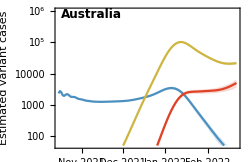
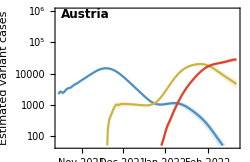
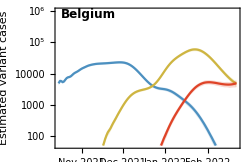
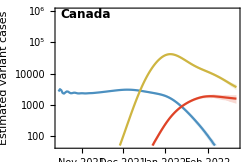
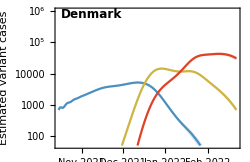
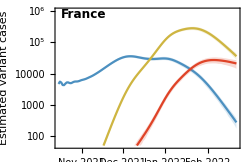
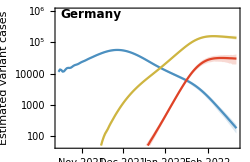
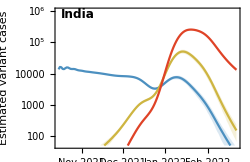
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries-split_variant-estimated-log-cases.png

```mathematica
yMaxForCountry[country_]:=Max[Flatten[Table[pGatherUpper[country,variant][[All,2]],{variant,variants}]]]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,yMaxForCountry[country]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{endDate,0}}]}]
]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,yMaxForCountry[country]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{endDate,0}}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,2,4}]]
```

```mathematica
panels=Map[countryPrevalencePlot,countries];
```

```mathematica
legendPanel=PointLegend[colors[[2;;4]],variants[[2;;4]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

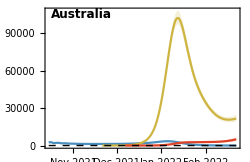
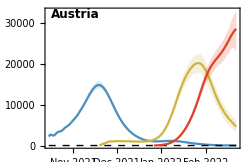
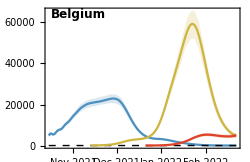
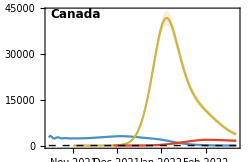
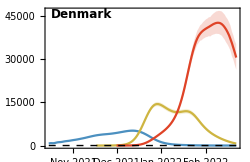
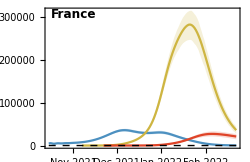
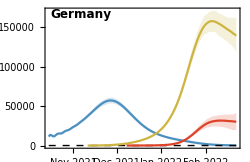
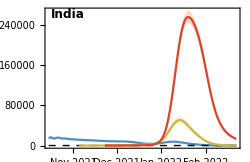
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries-split_variant-estimated-cases.png

Prevalence

```mathematica
Map[#->{pGather[#,"Omicron 21L"][[-1,1]],Round[pGather[#,"Omicron 21L"][[-1,2]]],Round[pGatherLower[#,"Omicron 21L"][[-1,2]]],Round[pGatherUpper[#,"Omicron 21L"][[-1,2]]]}&,countries]
```

{Australia→{2022-02-22,5006,3493,6503},Austria→{2022-02-22,28532,22996,32936},Belgium→{2022-02-22,4917,3714,6143},Canada→{2022-02-22,1582,1078,2047},Denmark→{2022-02-22,30641,26417,35301},France→{2022-02-22,21076,14169,26821},Germany→{2022-02-22,30145,19687,41066},India→{2022-02-22,13241,11516,15043},Indonesia→{2022-02-22,19085,13445,24101},Ireland→{2022-02-22,4473,3130,5852},Israel→{2022-02-22,3383,2001,4511},Italy→{2022-02-22,13282,8668,17673},Japan→{2022-02-22,2648,2156,3229},Netherlands→{2022-02-22,15396,11717,19524},New Zealand→{2022-02-22,2218,1411,3007},Norway→{2022-02-22,10615,9036,12229},Poland→{2022-02-22,4545,3527,5357},Portugal→{2022-02-22,4078,2595,5378},Romania→{2022-02-22,3081,2087,3943},Singapore→{2022-02-22,13547,10772,15990},South Africa→{2022-02-22,2371,2014,2748},Spain→{2022-02-22,10961,8021,13944},Sweden→{2022-02-22,4843,3975,5850},Switzerland→{2022-02-22,8210,5863,10437},Thailand→{2022-02-22,9039,6962,10906},United Kingdom→{2022-02-22,22295,18891,25440},USA→{2022-02-22,12160,8497,16281}}

## Frequency

```mathematica
fData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_freq-combined-"<>model<>".tsv"];
```

```mathematica
header=fData[[1]]
```

{date,location,variant,median_freq,freq_upper_95,freq_lower_95,freq_upper_80,freq_lower_80,freq_upper_50,freq_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_freq→4,freq_upper_95→5,freq_lower_95→6,freq_upper_80→7,freq_lower_80→8,freq_upper_50→9,freq_lower_50→10}

```mathematica
fData=Drop[fData,1];
```

```mathematica
fGather[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
fGatherLower[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
fGatherUpper[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryFrequencyPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=fGather[country,variant];
lowerSeries=fGatherLower[country,variant];
upperSeries=fGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant frequency"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,1}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Table[{i,ToString[Round[100*i]]<>"%"},{i,0,1,0.2}],Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{endDate,0}}]}]
]
```

```mathematica
countryFrequencyPlot[country_]:=Show[Table[variantCountryFrequencyPlot[country,variants[[i]],colors[[i]]],{i,2,4}]]
```

```mathematica
panels=Map[countryFrequencyPlot,countries];
```

```mathematica
legendPanel=PointLegend[colors[[2;;4]],variants[[2;;4]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

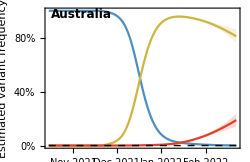
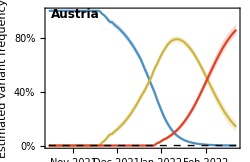
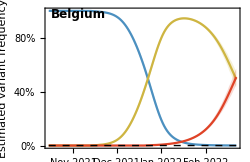
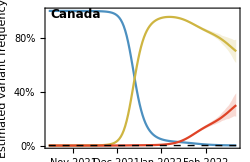
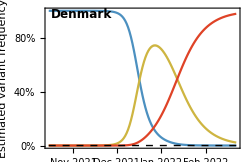
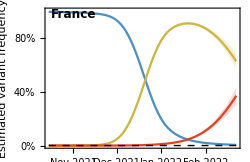
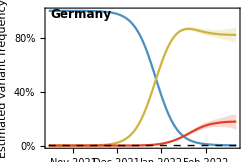
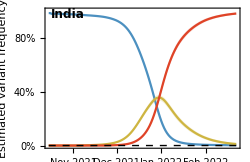
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-frequency.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries-split_variant-estimated-frequency.png

Frequency

```mathematica
Map[#->{fGather[#,"Omicron 21L"][[-1,1]],Round[fGather[#,"Omicron 21L"][[-1,2]],0.01],Round[fGatherLower[#,"Omicron 21L"][[-1,2]],0.01],Round[fGatherUpper[#,"Omicron 21L"][[-1,2]],0.01]}&,countries]
```

{Australia→{2022-02-22,0.19,0.14,0.24},Austria→{2022-02-22,0.86,0.82,0.9},Belgium→{2022-02-22,0.51,0.45,0.57},Canada→{2022-02-22,0.3,0.21,0.39},Denmark→{2022-02-22,0.98,0.97,0.98},France→{2022-02-22,0.37,0.3,0.42},Germany→{2022-02-22,0.18,0.12,0.23},India→{2022-02-22,0.98,0.97,0.99},Indonesia→{2022-02-22,0.34,0.26,0.41},Ireland→{2022-02-22,0.69,0.6,0.78},Israel→{2022-02-22,0.32,0.25,0.4},Italy→{2022-02-22,0.25,0.17,0.31},Japan→{2022-02-22,0.05,0.04,0.06},Netherlands→{2022-02-22,0.45,0.37,0.51},New Zealand→{2022-02-22,0.64,0.56,0.72},Norway→{2022-02-22,0.8,0.76,0.83},Poland→{2022-02-22,0.27,0.23,0.31},Portugal→{2022-02-22,0.32,0.21,0.4},Romania→{2022-02-22,0.28,0.21,0.35},Singapore→{2022-02-22,0.75,0.7,0.81},South Africa→{2022-02-22,0.94,0.9,0.97},Spain→{2022-02-22,0.4,0.32,0.48},Sweden→{2022-02-22,0.91,0.89,0.93},Switzerland→{2022-02-22,0.38,0.32,0.44},Thailand→{2022-02-22,0.47,0.39,0.55},United Kingdom→{2022-02-22,0.65,0.57,0.72},USA→{2022-02-22,0.21,0.12,0.29}}

## Phase diagrams

Convert to cases per 100k per day

```mathematica
perCapitaPGather[country_,variant_]:=Module[{popSize},
popSize=QuantityMagnitude[CountryData[country,"Population"]];
Map[{#[[1]],100000*#[[2]]/popSize}&,pGather[country,variant]]
]
```

```mathematica
compareWithDate[dateSeries1_, dateSeries2_] := Map[{#[[1, 1]], #[[1, 2]], #[[2, 2]]} &, DeleteCases[Map[{FirstCase[dateSeries1, x_ /; x[[1]] == #], FirstCase[dateSeries2, x_ /; x[[1]] == #]} &, dates], {x_, y_} /; x == Missing["NotFound"] || y == Missing["NotFound"]]]
```

```mathematica
phaseGather[country_,variant_]:=compareWithDate[perCapitaPGather[country,variant],rGather[country,variant]][[All,{2,3}]]
```

```mathematica
countryRPrevalencePhasePlot[country_]:=Module[{pairsOmicron21K,pairsOmicron21L},
pairsOmicron21K=phaseGather[country,"Omicron 21K"];
pairsOmicron21L=phaseGather[country,"Omicron 21L"];
ListLogLinearPlot[{pairsOmicron21K,{Last[pairsOmicron21K]},pairsOmicron21L,{Last[pairsOmicron21L]}},Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->True,PlotRange->{{2,700},
{-0.25,0.4}},Joined->{True,False},PlotMarkers->{None,{"•",Scaled[0.12]}},PlotStyle->{colors[[3]],colors[[3]],colors[[4]],colors[[4]]},
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
panels=Map[countryRPrevalencePhasePlot,countries];
```

```mathematica
legendPanel=PointLegend[colors[[3;;4]],variants[[3;;4]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Export["figures/"<>dataset<>"_variant-cases-vs-rt.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries-split_variant-cases-vs-rt.png